```mathematica
(*CSS221 Computer Graphics with Applications

Lab 1

Introduction into Mathematica*)
```

```mathematica
(*Problem1 Define a variable x equal to 3 and y equal to 2. Find x+y,x^2+y^2,x*y,x/y.Type every line in a different cell*)
```

```mathematica
x= 3
```

3

```mathematica
y = 2
```

2

```mathematica
x +y
```

5

```mathematica
x^2 + y^2
```

13

```mathematica
x*y
```

6

```mathematica
x/y
```

3/2

```mathematica
(*Problem2 First letters of the built in
functions are capitalized.Use[] around the arguments Find
Sqrt[5],Sqrt[5.],Exp[3.],SinPi3,ArcTan[Sqrt[3]] Assign these numerical values to varibles.Type them in different cells*)
xs1=Sqrt[5]
```

√5

```mathematica
xs2=Sqrt[5.]
```

2.23607

```mathematica
xe1=Exp[3.]
```

20.0855

```mathematica
xs3=Sin[Pi/3.]
```

0.866025

```mathematica
xa1=ArcTan[Sqrt[3]]
```

π/3

```mathematica
(*Find xs1+xs2+xe1+xs3+xa1*)
xs1+xs2+xe1+xs3+xa1
```

26.4709

```mathematica
(*Functions.2D plots*)
(*Problem3 Define f[x_]:=x^2+0.8 Note the underscore x_ denotes the argument.Call f[x] with x=3,x=Pi.x=1+t and x=Sin[t*Pi].Find f[f[4.5]]*)
f[x_]:=x^2+0.8
```

```mathematica
f[3]
```

9.8

```mathematica
f[Pi]
```

10.6696

```mathematica
f[1+t]
```

0.8+(1+t)^2

```mathematica
f[Sin[t*Pi]]
```

0.8+Sin[π t]^2

```mathematica
f[f[4.5]]
```

443.903

```mathematica
(*Problem(4) Define a function given by f[a_]:=Sin[a^2]+Cos[a] and call with a=1,a=1. and a=1.*Pi*)
f[a_]:=Sin[a^2]+Cos[a]
```

```mathematica
f[1]
```

Cos[1]+Sin[1]

```mathematica
f[1.]
```

1.38177

```mathematica
f[1.*Pi]
```

-1.4303

```mathematica
(*Problem(5) A function with more than one argument.Define the Function,f5[u_,v_]:=u/v Call f5[21,5]*)
f5[u_,v_]:=u/v
```

```mathematica
f5[21.,5.]
```

4.2

```mathematica
(*Problem(6) Plot f6[a_]:=a^2 as Plot[function,{x,xmin,xmax},Options],the argument x ranges from xmin to xmax.*)
f6[a_]:=a^2
```

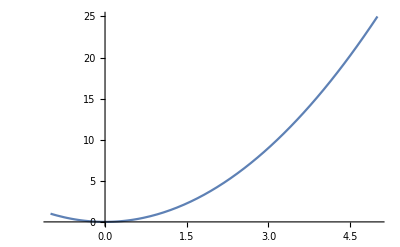

```mathematica
Plot[f6[a],{a,-1,5}]
```

```mathematica
(*Problem(6) Plotting several functions.1 Plot the function Sin[x^2] and Cos[x^2] with the range {0,2Pi},and with Axes->False.2 Use Options Axes->True,use PlotStyle->{Blue,Red} BaseStyle->{FontSize->14} and observe the difference*)
```

```mathematica
f81[x_] := Sin[x^2]
```

```mathematica
f82[x_] := Cos[x^2]
```

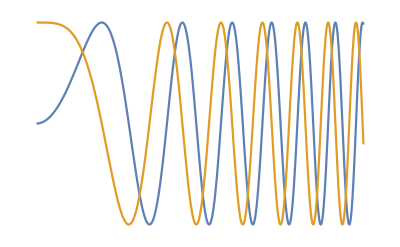

```mathematica
Plot[{f81[x],f82[x]},{x,0,2Pi},Axes->False]
```

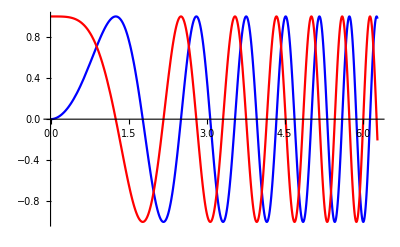

```mathematica
Plot[{f81[x],f82[x]},{x,0,2Pi},Axes->True,PlotStyle->{Blue,Red},BaseStyle->{FontSize->15}]
```

```mathematica
(*Problem (7) Plot three functions:Sin[x],Cos[x],1x+1 on interval {x,0,2Pi} using {Orange,Green,Blue}*)
f21[x_] := Sin[x]
```

```mathematica
f22[x_] := Cos[x]
```

```mathematica
f23[x_] := 1/(x+1)
```

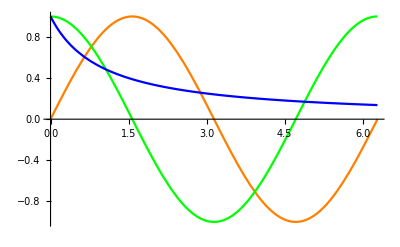

```mathematica
Plot[{f21[x],f22[x],f23[x]},{x,0,2Pi},Axes->True,PlotStyle->{Orange,Green,Blue},BaseStyle->{FontSize->15}]
```

```mathematica
(*Problem8 Plot a parametric function using the ParametricPlot*)(*Parametric function is specified by a pair xt,yt of a parametric variable t.Define x[t_]:=Cos[7t]Cos[11t],y[t_]:=Cos[7t]Sin[11t],t ranges from 0 to 2Pi,Use AspectRatio->1. It specifies the ratio of height to width for a plot.*)
```

```mathematica
x10[t_]:=Cos[7 t] Cos[11 t]
```

```mathematica
y10[t_]:=Cos[7 t] Sin[11 t]
```

```mathematica
p10[t_]:={x10[t],y10[t]}
```

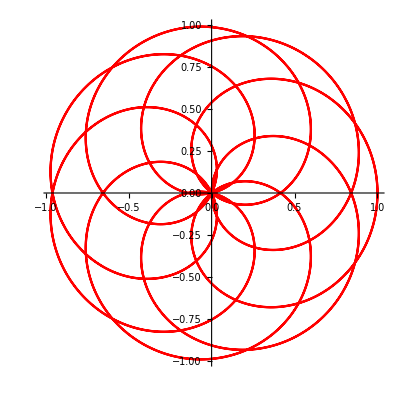

```mathematica
ParametricPlot[p10[t],{t,0,2Pi},PlotStyle->Red,AspectRatio->1]
```

```mathematica
(*Problem9 Plot the following two parametric functions x111[t_]:=Sin[t];y111[t_]:=Cos[t^4] and x112[t_]:=Sin[t^2];
y112[t_]:=Cos[11*t]+Sqrt[t] on one graph,{t,-2,2},use PlotStyle->{Blue,Red} Background->LightYellow AspectRatio->1*)
```

```mathematica
x111[t_] := Sin[t]
```

```mathematica
y111[t_]:=Cos[t^4]
```

```mathematica
x112[t_] := Sin[t^2]
```

```mathematica
y112[t_] := Cos[11*t]+Sqrt[t]
```

```mathematica
p111[t_]:={x111[t],y111[t]}
```

```mathematica
p112[t_]:={x112[t],y112[t]}
```

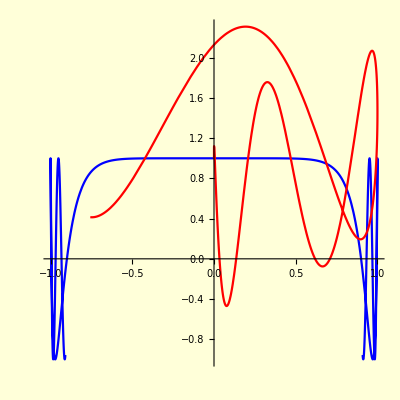

```mathematica
ParametricPlot[{p111[t],p112[t]},{t,-2,2},PlotStyle->{Blue,Red},Background->LightYellow,AspectRatio->1]
```

```mathematica
(*2D Plotting lists*)
(*Problem10 ListPlot is designed for plotting a discrete data.The list is composed of the x and y coordinates.The size and color of the points are controlled by the PlotStyle Options.Practice with the following list*)
G={{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}
```

{{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}

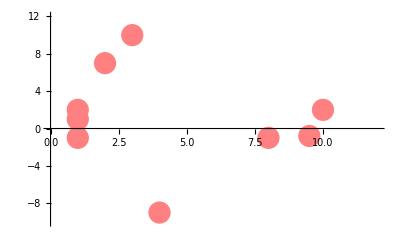

```mathematica
Plot1=ListPlot[G,PlotStyle->{PointSize[0.04],Pink},PlotRange->{{0,12},{-10,12}}]
```

```mathematica
(*Note that the above plot has been now associated with the variable Plot1*)
(*Problem11 Plot list G again with options PlotJoined->True,PlotStyle->{Green,Thickness[0.01]},PlotRange->{{0,12},{-10,12}} and superimpose Plot1 and Plot2*)
```

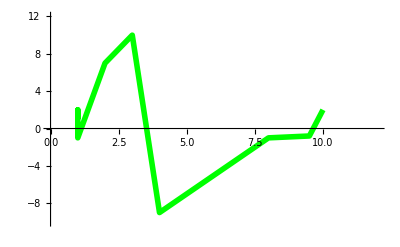

```mathematica
Plot2=ListPlot[G,Joined->True,PlotStyle->{Green,Thickness[0.01]},PlotRange->{{0,12},{-10,12}}]
```

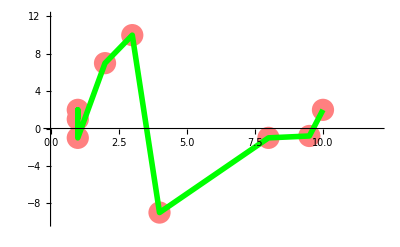

```mathematica
(*Superimpose Plot1 and Plot2*)
Show[Plot1,Plot2]
```

```mathematica
(*Animating 2D Plots*)
(*Problem12 Use Animate[Plot[function],{parameter,pmin,pmax,step}] to animate Cos[n x] {x,0,2Pi} {n,1,6,1} from 1 to 6 with the step 1*)
f16[x_,n_]:=Cos[n*x]
```

```mathematica
Animate[Plot[f16[x,n],{x,0,2Pi}],{n,1,6,1},AnimationRunning->False]
```

```mathematica
(*Problem13 Use Animate[Plot[function],{parameter,pmin,pmax,step}] to animate two explicit functions Cosn x10 and Sin[n^2 x] {x,0,5Pi} {n,1,10,1}*)
f131[x_,n_]:=Cos[n x/10]
```

```mathematica
f132[x_,n_]:=Sin[n^2 x]
```

```mathematica
Animate[Plot[{f131[x,n],f132[x,n]},{x,0,5Pi}],{n,1,10,1},AnimationRunning->False]
```

```mathematica
(*Problem14 Use ParametricPlot to animate a parametric plot of a function given by xp[t_,n_]:=Sin[2t*n],yp[t_,n_]:=Cost^2*n10,{t,0,5} {n,1,10,1}.Use PlotPoints->100*)
```

```mathematica
xp[t_,n_]:=Sin[2t*n]
```

```mathematica
yp[t_,n_]:=Cos[t^2*n/10]
```

```mathematica
Animate[ParametricPlot[{xp[t,n],yp[t,n]},{t,0,5},PlotPoints->100],{n,1,10,1},AnimationRunning->False]
```

```mathematica
(*3D Plots*)
(*Problem15 Plot a 3D function given by Sin[x^2-y^2] on {x,-1,3} {y,-2,2} and note options such as AxesLabel and the number of points in each direction given by PlotPoints.*)
```

```mathematica
f19[x_,y_]:=Sin[x^2-y^2]
```

```mathematica
Plot3D[f19[x,y],{x,-1,3},{y,-2,2},PlotPoints->{20,20},AxesLabel->{"Length","Width","Height"}]
```

-Graphics3D-

```mathematica
(*Problem16 Animate a family of surfaces given by Sin[x+y*n] on {x,0,4},{y,0,2} {n,1,15,2}*)
f21[x_,y_,n_]:=Sin[x+y*n]
```

```mathematica
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotPoints->40,PlotLabel->"Animation"],{n,1,15,2},AnimationRunning->False]
```

```mathematica
(*The entire set of options is given using:*)
```

```mathematica
(*Problem17 Beatify the graph above.Select 3 additional options or change the existing ones and animate the result.Your graph may look different*)
```

```mathematica
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotPoints->40,PlotLabel->"Animation",ColorFunction->"BlueGreenYellow",MeshStyle->Orange],{n,1,15,2},AnimationRunning->False]
```

```mathematica
(*Your graph may look different*)
(*Problem18 Using ParametricPlot3D plot a spiral below*)
```

```mathematica
x22[u_]:=Sin[u]
```

```mathematica
y22[u_]:=Cos[u]
```

```mathematica
z22[u_]:=u/10
```

```mathematica
spiral[u_]:={x22[u],y22[u],z22[u]}
```

```mathematica
ParametricPlot3D[spiral[u],{u,0,20}]
```

-Graphics3D-

```mathematica
(*Problem 19 Beatify the graph using 3 new options.Use Options[ParametricPlot3D] and Mathematica help,for example,change PlotStyle->AxesLabel->and Opacity.*)
(*The entire set of options is given using:*)
(*your graphs may look different*)
ParametricPlot3D[spiral[u],{u,0,20},ColorFunction->"Rainbow",PlotStyle->{Thick},Opacity[0.5]]
```

ParametricPlot3D::nonopt: Options expected (instead of Opacity[0.5]) beyond position 3 in ParametricPlot3D[spiral[u],{u,0,20},ColorFunction→Rainbow,PlotStyle→{Thick},Opacity[0.5]]. An option must be a rule or a list of rules.

```mathematica
ParametricPlot3D[spiral[u],{u,0,20},ColorFunction->"BlueGreenYellow",PlotStyle->{Thick,Opacity[0.5]}]
```

-Graphics3D-

```mathematica
(*Problem20 Animate a parametric function x23[u_,v_]:=u y23[u_,v_]:=v z23[u_,v_,n_]:=n*u^2+v^210 on 1 graph,n is the animation parameter {n,1,3,0.5}.Fix the PlotRange->{{-5,5},{-5,5},{0,10}} to avoid changing the graphics box.Use PlotPoints->20*)
x23[u_,v_]:=u
```

```mathematica
y23[u_,v_]:=v
```

```mathematica
z23[u_,v_,n_]:=n*(u^2+v^2)/10
```

```mathematica
p23[u_,v_,n_]:={x23[u,v],y23[u,v],z23[u,v,n]}
```

```mathematica
Animate[ParametricPlot3D[p23[u,v,n],{u,-5,5},{v,-5,5},Mesh->True,PlotRange->{{-5,5},{-5,5},{0,10}},PlotPoints->20],{n,1,3,0.5},AnimationRunning->False]
```

ParametricPlot::nonopt: Options expected (instead of AspectRatio→1) beyond position 3 in ParametricPlot[p10[t],{t,0,2 π},PlotStyle→Red,AspectRatio→1]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of Axes→True) beyond position 2 in Plot[{f81[x],f82[x]},{x,0,2 π},Axes→True,PlotStyle→{Blue,Red},BaseStyle→{FontSize→14}]. An option must be a rule or a list of rules.